## 非线性方程求解

### 二分法

```mathematica
dichotomy[f_,interval_,eps_]:=FixedPoint[
  With[{a=Min[#],b=Max[#],c=Mean[#]},
   Which[
    f[a]f[c]<0,{a,c},
    f[c]f[b]<0,{c,b},
    (*既不在左半区间，也不在右半区间，直接抛出中点*)
    True,Throw[{c}]
   ]
  ]&,interval,
  SameTest->(Abs[#⟦1⟧-#⟦2⟧]<eps&)
 ]//Catch//Mean
```

```mathematica
dichotomy[x↦Sin[x]-x^2/2,{1.,2.},0.5*^-5]
```

1.40441

### 牛顿法/改进的牛顿法

```mathematica
newton[f_,x0_,r_:1,maxIter_:1000]:=With[
  (*符号计算并化简牛顿法迭代函数*)
  {φ=x↦Evaluate@FullSimplify[x-r f[x]/f'[x]]},
  FixedPoint[φ,x0,maxIter,SameTest->Equal]
 ]
```

```mathematica
newton[x↦x ⅇ^x-1,0.5]
```

0.567143

```mathematica
newton[x↦x^3-x-1,1.]
```

1.32472

```mathematica
newton[x↦(x-1)^2(2x-1),0.45]
```

0.5

```mathematica
newton[x↦(x-1)^2(2x-1),0.65]
```

0.5

```mathematica
newton[x↦(x-1)^2(2x-1),0.55,2,1*^6]
```

0.500177

```mathematica
newtonMonitored[f_,x0_,r_:1,maxIter_:1000,monitor_:None]:=With[
  {φ=x↦Evaluate@FullSimplify[x-r f[x]/f'[x]]},
  FixedPoint[(monitor[#];φ[#])&,x0,maxIter,SameTest->Equal]
 ]
```

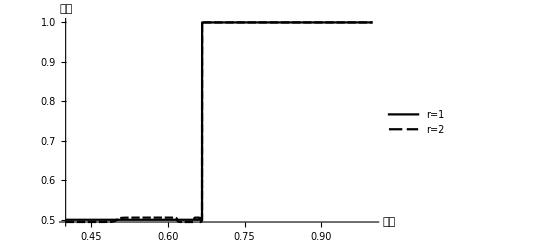

```mathematica
Plot[{newton[x↦(x-1)^2(2x-1),x0,1],newton[x↦(x-1)^2(2x-1),x0,2]},{x0,0.4,1},AxesLabel->{"初值","终值"},PlotLegends->{"r=1","r=2"},PlotTheme->"Monochrome"]
```

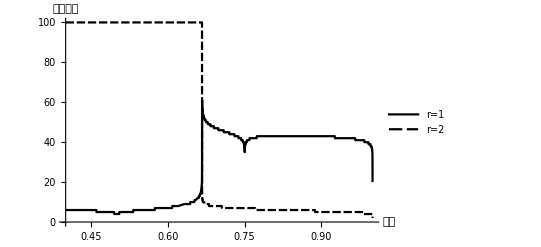

```mathematica
Plot[{Block[{step=0},newtonMonitored[x↦(x-1)^2(2x-1),x0,1,100,step++&];step],
Block[{step=0},newtonMonitored[x↦(x-1)^2(2x-1),x0,2,100,step++&];step]},
{x0,0.4,1},AxesLabel->{"初值","迭代次数"},PlotLegends->{"r=1","r=2"},PlotTheme->"Monochrome"]
```

### 割线法

```mathematica
secant[f_,{x0_,x1_},maxIter_:1000]:=NestWhile[
  With[{xkk=#⟦1⟧,xk=#⟦2⟧},
   {xk,
    xk-f[xk]/(f[xk]-f[xkk])(xk-xkk)
   }]&,{x0,x1},
  Apply[Unequal],1,
  maxIter
 ]⟦2⟧
```

```mathematica
secant[x↦x ⅇ^x-1,{0.4,0.6}]
```

0.567143

### 拟牛顿法

```mathematica
jacobian[f_, dim_] := With[{vars = Table[Unique["var$$"], dim]},
  Function[Evaluate@vars, Evaluate[D[f@@vars, {vars}]]]
 ]
```

```mathematica
quasiNewton[f_,dim_,x0_,maxIter_:1000]:=
 With[{h0=Inverse@*jacobian[f,dim]@@x0},
  FixedPoint[
   Block[{x=#⟦1⟧,h=#⟦2⟧,fx,xnext,r,y,rhy},
    fx=f@@x;
    xnext=x-h.fx;
    r=xnext-x;y=f@@xnext-fx;
    rhy=r.h.y;
    {xnext,
     h+KroneckerProduct[(r-h.y),(r.h)/rhy]}
    ]&,
   {x0,h0},maxIter,
   SameTest->(#1⟦1⟧==#2⟦1⟧&)
  ]⟦1⟧
 ]
```

```mathematica
quasiNewton[{x,y,z}↦{x y-z^2-1,x y z+y^2-x^2-2,ⅇ^x+z-ⅇ^y-3},3,{1.,1.,1.}]
```

{1.77767,1.42396,1.23747}

## 高斯列主元消去法

### 高斯消去法

```mathematica
eliminate[mat_?MatrixQ] := Module[{a = mat},
  Do[
   (*直接消元*)
   a⟦k+1;;, k;;⟧ -= a⟦k+1;;, {k}⟧.a⟦{k}, k;;⟧/a⟦k, k⟧,
   {k, Min@Dimensions@a - 1}
   ];
  a
 ]
```

### 高斯列主元消去

```mathematica
eliminatePE[mat_?MatrixQ] := Module[{a = mat},
  Do[
   With[
    {r = k-1+First@Ordering[Abs@a⟦k;;, k⟧, 1, GreaterEqual]},(*找主元*)
    a⟦{k,r},All⟧ = a⟦{r,k},All⟧(*交换*)
   ];
   a⟦k+1;;, k;;⟧ -= a⟦k+1;;, {k}⟧.a⟦{k}, k;;⟧/a⟦k, k⟧,
   {k, Min@Dimensions@a - 1}
   ];
  a
  ]
```

### 求解

```mathematica
eliminationSolve[a_?MatrixQ,b_?VectorQ,eliminator_]:=
 With[{aa=eliminator[MapThread[Append,{a,b}]],n=Length[aᵀ]},
  Module[{x=ConstantArray[0,n]},
   Do[(*回带*)
    x⟦k⟧=(aa⟦k,n+1⟧-∑_(j=1+k)^n x⟦j⟧ aa⟦k,j⟧)/aa⟦k,k⟧,
    {k,n,1,-1}
   ];
   x
  ]
 ]
```

```mathematica
eliminationSolve[({{10.^-8, 2, 3}, {-1, 3.712, 4.623}, {-2, 1.072, 5.643}}),{1,2,3},eliminate]
```

{-0.491058,-0.0508861,0.367257}

```mathematica
eliminationSolve[({{10^-8, 2, 3}, {-1, 3.712, 4.623}, {-2, 1.072, 5.643}}),{1,2,3},eliminatePE]
```

{-0.491058,-0.0508861,0.367257}

```mathematica
eliminationSolve[({{4, -2, 4}, {-2, 17, 10}, {-4, 10, 9}}),{10,3,7},eliminate]
```

{11/56,-25/28,13/7}

```mathematica
eliminationSolve[({{4, -2, 4}, {-2, 17, 10}, {-4, 10, 9}}),{10,3,7},eliminatePE]
```

{11/56,-25/28,13/7}